```mathematica
FindInstance[{E^x == k, E^x == k x},{x,k}]
```

{{x→1,k→ⅇ}}

```mathematica
(*Param first*)
```

```mathematica
(*if k has a nice expr*)
```

```mathematica
Solve[E^x== k x,k]
```

{{k→ⅇ^x/x}}

```mathematica
Manipulate[Plot[{ⅇ^x/x,a},{x,-10,10},PlotRange->10],{a,-10,10}]
```

```mathematica
{x,ⅇ^x/x}/.Solve[D[ⅇ^x/x,x] == 0,x]
```

{{1,ⅇ}}

```mathematica
(*if k has an ugly expr*)
```

```mathematica
Solve[k/(x - 2) == √(4 - k x),k]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{k→1/2 (-x (4-4 x+x^2)-(-2+x) √(16+4 x^2-4 x^3+x^4))},{k→1/2 (-x (4-4 x+x^2)+(-2+x) √(16+4 x^2-4 x^3+x^4))}}

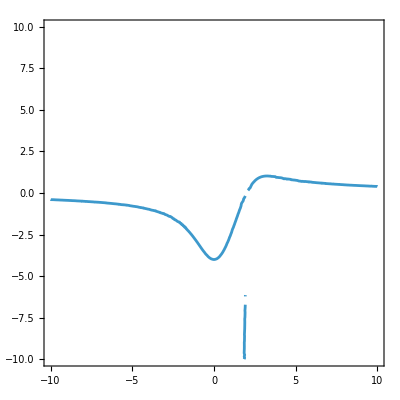

```mathematica
ContourPlot[k/(x - 2) == √(4 - k x),{x,-10,10},{k,-10,10},Axes->True]
```

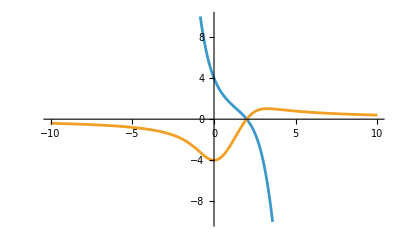

```mathematica
Plot[{1/2 (-x (4-4 x+x^2)-(-2+x) √(16+4 x^2-4 x^3+x^4)),1/2 (-x (4-4 x+x^2)+(-2+x) √(16+4 x^2-4 x^3+x^4))},{x,-10,10},PlotRange->10]
```

```mathematica
Manipulate[Plot[{k/(x - 2) , √(4 - k x)},{x,-10,10},PlotRange->10],{k,-10,10}]
```

```mathematica
{x,1/2 (-x (4-4 x+x^2)+(-2+x) √(16+4 x^2-4 x^3+x^4))}/.NSolve[D[1/2 (-x (4-4 x+x^2)+(-2+x) √(16+4 x^2-4 x^3+x^4)),x] == 0,x]
```

{{3.27005,1.02431},{0.,-4.}}